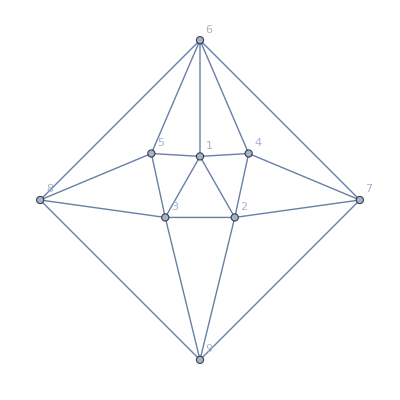

```mathematica
kempe=Graph[{1<->2,2<->3,3<->1,1<->4,4<->2,1<->5,5<->3,1<->6,4<->6,5<->6,6<->7,4<->7,7<->2,8<->3,8<->6,5<->8,7<->9,8<->9,9<->2,9<->3},VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ChromaticPolynomial[kempe,3]
```

0

```mathematica
solsk=ToVarsLogical[kempe,True];
```

```mathematica
TableForm[Map[SolutionToPartition2[#,{6,8,5,1,4,7}]&,solsk]//Sort,TableDepth->1]
```

{{},{6},{5,4},{8,1,7}}
{{},{6},{5,4},{8,1,7}}
{{},{6},{8,1,7},{5,4}}
{{},{6},{8,1,7},{5,4}}
{{},{5,4},{6},{8,1,7}}
{{},{5,4},{6},{8,1,7}}
{{},{5,4},{8,1,7},{6}}
{{},{5,4},{8,1,7},{6}}
{{},{8,1,7},{6},{5,4}}
{{},{8,1,7},{6},{5,4}}
{{},{8,1,7},{5,4},{6}}
{{},{8,1,7},{5,4},{6}}
{{4},{5},{6},{8,1,7}}
{{4},{5},{6},{8,1,7}}
{{4},{5},{6},{8,1,7}}
{{4},{5},{8,1,7},{6}}
{{4},{5},{8,1,7},{6}}
{{4},{5},{8,1,7},{6}}
{{4},{6},{5},{8,1,7}}
{{4},{6},{5},{8,1,7}}
{{4},{6},{5},{8,1,7}}
{{4},{6},{8,1,7},{5}}
{{4},{6},{8,1,7},{5}}
{{4},{6},{8,1,7},{5}}
{{4},{8,1,7},{5},{6}}
{{4},{8,1,7},{5},{6}}
{{4},{8,1,7},{5},{6}}
{{4},{8,1,7},{6},{5}}
{{4},{8,1,7},{6},{5}}
{{4},{8,1,7},{6},{5}}
{{5},{4},{6},{8,1,7}}
{{5},{4},{6},{8,1,7}}
{{5},{4},{6},{8,1,7}}
{{5},{4},{8,1,7},{6}}
{{5},{4},{8,1,7},{6}}
{{5},{4},{8,1,7},{6}}
{{5},{6},{4},{8,1,7}}
{{5},{6},{4},{8,1,7}}
{{5},{6},{4},{8,1,7}}
{{5},{6},{8,1,7},{4}}
{{5},{6},{8,1,7},{4}}
{{5},{6},{8,1,7},{4}}
{{5},{8,1,7},{4},{6}}
{{5},{8,1,7},{4},{6}}
{{5},{8,1,7},{4},{6}}
{{5},{8,1,7},{6},{4}}
{{5},{8,1,7},{6},{4}}
{{5},{8,1,7},{6},{4}}
{{6},{},{5,4},{8,1,7}}
{{6},{},{5,4},{8,1,7}}
{{6},{},{8,1,7},{5,4}}
{{6},{},{8,1,7},{5,4}}
{{6},{4},{5},{8,1,7}}
{{6},{4},{5},{8,1,7}}
{{6},{4},{5},{8,1,7}}
{{6},{4},{8,1,7},{5}}
{{6},{4},{8,1,7},{5}}
{{6},{4},{8,1,7},{5}}
{{6},{5},{4},{8,1,7}}
{{6},{5},{4},{8,1,7}}
{{6},{5},{4},{8,1,7}}
{{6},{5},{8,1,7},{4}}
{{6},{5},{8,1,7},{4}}
{{6},{5},{8,1,7},{4}}
{{6},{7},{5,4},{8,1}}
{{6},{7},{8,1},{5,4}}
{{6},{8},{1,7},{5,4}}
{{6},{8},{5,4},{1,7}}
{{6},{1,7},{8},{5,4}}
{{6},{1,7},{5,4},{8}}
{{6},{5,4},{},{8,1,7}}
{{6},{5,4},{},{8,1,7}}
{{6},{5,4},{7},{8,1}}
{{6},{5,4},{8},{1,7}}
{{6},{5,4},{1,7},{8}}
{{6},{5,4},{8,1},{7}}
{{6},{5,4},{8,1,7},{}}
{{6},{5,4},{8,1,7},{}}
{{6},{8,1},{7},{5,4}}
{{6},{8,1},{5,4},{7}}
{{6},{8,1,7},{},{5,4}}
{{6},{8,1,7},{},{5,4}}
{{6},{8,1,7},{4},{5}}
{{6},{8,1,7},{4},{5}}
{{6},{8,1,7},{4},{5}}
{{6},{8,1,7},{5},{4}}
{{6},{8,1,7},{5},{4}}
{{6},{8,1,7},{5},{4}}
{{6},{8,1,7},{5,4},{}}
{{6},{8,1,7},{5,4},{}}
{{7},{6},{5,4},{8,1}}
{{7},{6},{8,1},{5,4}}
{{7},{5,4},{6},{8,1}}
{{7},{5,4},{8,1},{6}}
{{7},{8,1},{6},{5,4}}
{{7},{8,1},{5,4},{6}}
{{8},{6},{1,7},{5,4}}
{{8},{6},{5,4},{1,7}}
{{8},{1,7},{6},{5,4}}
{{8},{1,7},{5,4},{6}}
{{8},{5,4},{6},{1,7}}
{{8},{5,4},{1,7},{6}}
{{1,7},{6},{8},{5,4}}
{{1,7},{6},{5,4},{8}}
{{1,7},{8},{6},{5,4}}
{{1,7},{8},{5,4},{6}}
{{1,7},{5,4},{6},{8}}
{{1,7},{5,4},{8},{6}}
{{5,4},{},{6},{8,1,7}}
{{5,4},{},{6},{8,1,7}}
{{5,4},{},{8,1,7},{6}}
{{5,4},{},{8,1,7},{6}}
{{5,4},{6},{},{8,1,7}}
{{5,4},{6},{},{8,1,7}}
{{5,4},{6},{7},{8,1}}
{{5,4},{6},{8},{1,7}}
{{5,4},{6},{1,7},{8}}
{{5,4},{6},{8,1},{7}}
{{5,4},{6},{8,1,7},{}}
{{5,4},{6},{8,1,7},{}}
{{5,4},{7},{6},{8,1}}
{{5,4},{7},{8,1},{6}}
{{5,4},{8},{6},{1,7}}
{{5,4},{8},{1,7},{6}}
{{5,4},{1,7},{6},{8}}
{{5,4},{1,7},{8},{6}}
{{5,4},{8,1},{6},{7}}
{{5,4},{8,1},{7},{6}}
{{5,4},{8,1,7},{},{6}}
{{5,4},{8,1,7},{},{6}}
{{5,4},{8,1,7},{6},{}}
{{5,4},{8,1,7},{6},{}}
{{8,1},{6},{7},{5,4}}
{{8,1},{6},{5,4},{7}}
{{8,1},{7},{6},{5,4}}
{{8,1},{7},{5,4},{6}}
{{8,1},{5,4},{6},{7}}
{{8,1},{5,4},{7},{6}}
{{8,1,7},{},{6},{5,4}}
{{8,1,7},{},{6},{5,4}}
{{8,1,7},{},{5,4},{6}}
{{8,1,7},{},{5,4},{6}}
{{8,1,7},{4},{5},{6}}
{{8,1,7},{4},{5},{6}}
{{8,1,7},{4},{5},{6}}
{{8,1,7},{4},{6},{5}}
{{8,1,7},{4},{6},{5}}
{{8,1,7},{4},{6},{5}}
{{8,1,7},{5},{4},{6}}
{{8,1,7},{5},{4},{6}}
{{8,1,7},{5},{4},{6}}
{{8,1,7},{5},{6},{4}}
{{8,1,7},{5},{6},{4}}
{{8,1,7},{5},{6},{4}}
{{8,1,7},{6},{},{5,4}}
{{8,1,7},{6},{},{5,4}}
{{8,1,7},{6},{4},{5}}
{{8,1,7},{6},{4},{5}}
{{8,1,7},{6},{4},{5}}
{{8,1,7},{6},{5},{4}}
{{8,1,7},{6},{5},{4}}
{{8,1,7},{6},{5},{4}}
{{8,1,7},{6},{5,4},{}}
{{8,1,7},{6},{5,4},{}}
{{8,1,7},{5,4},{},{6}}
{{8,1,7},{5,4},{},{6}}
{{8,1,7},{5,4},{6},{}}
{{8,1,7},{5,4},{6},{}}

```mathematica
Table[{StirlingS2[n,n-1],StirlingS2[n-1,n-1],2*StirlingS2[n,n-1]-StirlingS2[n-1,1]},{n,2,10}]
```

{{1,1,1},{3,1,5},{6,1,11},{10,1,19},{15,1,29},{21,1,41},{28,1,55},{36,1,71},{45,1,89}}

```mathematica
TableForm[Table[n+1->Table[{StirlingS2[n+1,n-k],2*StirlingS2[n,n-k]-StirlingS2[n-1,n-1-(k-1)],StirlingS2[n+1,n-k]-(2*StirlingS2[n,n-k]-StirlingS2[n-1,n-1-(k-1)])},{k,0,n}],{n,2,10}],TableDepth->1]
```

3→{{3,2,1},{1,1,0},{0,0,0}}
4→{{6,2,4},{7,5,2},{1,1,0},{0,0,0}}
5→{{10,2,8},{25,11,14},{15,11,4},{1,1,0},{0,0,0}}
6→{{15,2,13},{65,19,46},{90,44,46},{31,23,8},{1,1,0},{0,0,0}}
7→{{21,2,19},{140,29,111},{350,120,230},{301,155,146},{63,47,16},{1,1,0},{0,0,0}}
8→{{28,2,26},{266,41,225},{1050,265,785},{1701,635,1066},{966,512,454},{127,95,32},{1,1,0},{0,0,0}}
9→{{36,2,34},{462,55,407},{2646,511,2135},{6951,1960,4991},{7770,3052,4718},{3025,1631,1394},{255,191,64},{1,1,0},{0,0,0}}
10→{{45,2,43},{750,71,679},{5880,896,4984},{22827,5026,17801},{42525,12852,29673},{34105,13839,20266},{9330,5084,4246},{511,383,128},{1,1,0},{0,0,0}}
11→{{55,2,53},{1155,89,1066},{11880,1464,10416},{63987,11298,52689},{179487,43008,136479},{246730,78099,168631},{145750,60440,85310},{28501,15635,12866},{1023,767,256},{1,1,0},{0,0,0}}

```mathematica
TableForm[Table[n+1->Table[{StirlingS2[n+1,n-k],3*StirlingS2[n,n-k]-2*StirlingS2[n-1,n-1-(k-1)],StirlingS2[n+1,n-k]-(3*StirlingS2[n,n-k]-2*StirlingS2[n-1,n-1-(k-1)])},{k,0,n}],{n,2,10}],TableDepth->2]
```

3→{{3,3,0},{1,1,0},{0,0,0}}
4→{{6,3,3},{7,7,0},{1,1,0},{0,0,0}}
5→{{10,3,7},{25,16,9},{15,15,0},{1,1,0},{0,0,0}}
6→{{15,3,12},{65,28,37},{90,63,27},{31,31,0},{1,1,0},{0,0,0}}
7→{{21,3,18},{140,43,97},{350,175,175},{301,220,81},{63,63,0},{1,1,0},{0,0,0}}
8→{{28,3,25},{266,61,205},{1050,390,660},{1701,920,781},{966,723,243},{127,127,0},{1,1,0},{0,0,0}}
9→{{36,3,33},{462,82,380},{2646,756,1890},{6951,2870,4081},{7770,4403,3367},{3025,2296,729},{255,255,0},{1,1,0},{0,0,0}}
10→{{45,3,42},{750,106,644},{5880,1330,4550},{22827,7406,15421},{42525,18753,23772},{34105,19908,14197},{9330,7143,2187},{511,511,0},{1,1,0},{0,0,0}}
11→{{55,3,52},{1155,133,1022},{11880,2178,9702},{63987,16716,47271},{179487,63189,116298},{246730,113673,133057},{145750,86775,58975},{28501,21940,6561},{1023,1023,0},{1,1,0},{0,0,0}}